## Definitions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/stephan_schiffels/dev/celtic_relationship_analysis

```mathematica
CreateDirectory["Figures"]
```

CreateDirectory::eexist: /Users/stephan_schiffels/dev/celtic_relationship_analysis/Figures already exists.

$Failed

```mathematica
readStanDataset[filename_]:=Module[{rawD},
	rawD=Import[filename]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&];
	Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
]
```

```mathematica
hochdorfBurialDateDist=NormalDistribution[-530,6];
aspergBurialDateDist=NormalDistribution[-490,6];
```

```mathematica
hochdorfAgeDist=NormalDistribution[45,6];
aspergAgeDist=NormalDistribution[30,6];
```

```mathematica
mothersAgeDist=NormalDistribution[30,6];
```

```mathematica
mothersAgeDist2=GammaDistribution[2.313854479923621,3.8142370826527583,1,14.374410438813113];
```

## Prior distributions

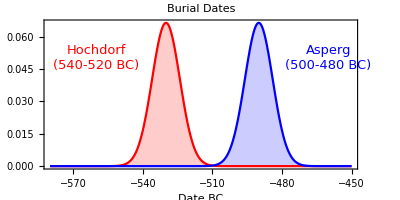

```mathematica
p=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Date BC",None},
Epilog->{
Text[Style["Hochdorf\n(540-520 BC)",Red,13],{-560,0.05}],
Text[Style["Asperg\n(500-480 BC)",Blue,13],{-460,0.05}]
},
PlotLabel->"Burial Dates",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/burialDates.pdf",p]
Export["Figures/burialDates.png",p]
```

Figures/burialDates.pdf

Figures/burialDates.png

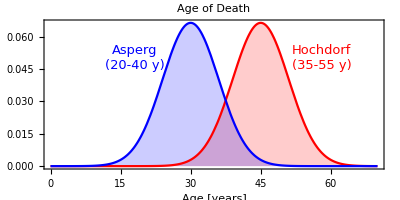

```mathematica
p=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age [years]",None},
Epilog->{
Text[Style["Hochdorf\n(35-55 y)",Red,13],{58,0.05}],
Text[Style["Asperg\n(20-40 y)",Blue,13],{18,0.05}]
},
PlotLabel->"Age of Death",AspectRatio->1/2]
```

```mathematica
Export["Figures/ages.pdf",p]
Export["Figures/ages.png",p]
```

Figures/ages.pdf

Figures/ages.png

```mathematica
n=10000;
hochdorfBirthDateSamples=RandomVariate[hochdorfBurialDateDist,n]-RandomVariate[hochdorfAgeDist,n];
aspergBirthDateSamples=RandomVariate[aspergBurialDateDist,n]-RandomVariate[aspergAgeDist,n];
```

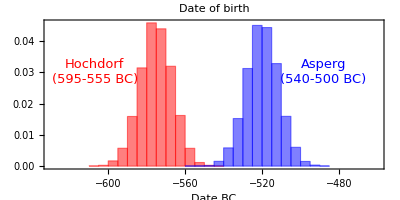

```mathematica
p=Histogram[{hochdorfBirthDateSamples,aspergBirthDateSamples},Automatic,"PDF",PlotRange->{{-630,-460},All},ChartStyle->{Red,Blue},
Frame->{True,False,False,False},
FrameLabel->{"Date BC",None},
Epilog->{
Text[Style["Hochdorf\n(595-555 BC)",Red,13],{-607,0.03}],
Text[Style["Asperg\n(540-500 BC)",Blue,13],{-488,0.03}]
},
PlotLabel->"Date of birth",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/birthDates.pdf",p]
```

Figures/birthDates.pdf

```mathematica
Quantile[hochdorfBirthDateSamples,{0.01,0.99}]
Quantile[aspergBirthDateSamples,{0.01,0.99}]
```

{-594.964,-556.097}

{-539.658,-500.127}

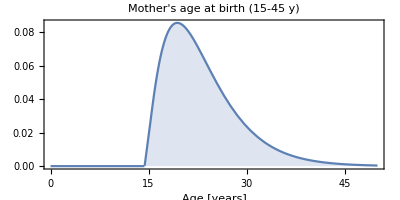

```mathematica
p=Plot[PDF[mothersAgeDist2,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age [years]",None},
PlotLabel->"Mother's age at birth (15-45 y)",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/mothersAge.pdf",p]
Export["Figures/mothersAge.png",p]
```

Figures/mothersAge.pdf

Figures/mothersAge.png

## Posterior distributions figures for DAG seminar

### Sibling model

```mathematica
dat=readStanDataset["model_siblings_output.csv"];
```

```mathematica
dat[First,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,burial_h,burial_a,age_h,age_a,age_m_h,birth_date_mother,age_m_a}

```mathematica
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal
```

<|lp__→3.09437,accept_stat__→1,stepsize__→0.635902,treedepth__→2,n_leapfrog__→3,divergent__→0,energy__→-0.167566,burial_h→-523.434,burial_a→-498.861,age_h→39.0748,age_a→37.7177,age_m_h→19.6753,birth_date_mother→-582.184,age_m_a→45.6058|>

```mathematica
maxLLvalue=
LogLikelihood[NormalDistribution[-530,6],{maxLLparams[["burial_h"]]}]+
LogLikelihood[NormalDistribution[-490,6],{maxLLparams[["burial_a"]]}]+
LogLikelihood[NormalDistribution[45,6],{maxLLparams[["age_h"]]}]+
LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_a"]]}]+LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_m_a"]],maxLLparams[["age_m_h"]]}]
```

-24.1314

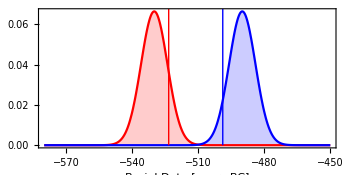

```mathematica
maxLLh=maxLLparams["burial_h"];
maxLLa=maxLLparams["burial_a"];
p1=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Burial Date [years BC]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

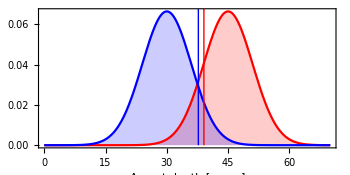

```mathematica
maxLLh=maxLLparams["age_h"];
maxLLa=maxLLparams["age_a"];
p2=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

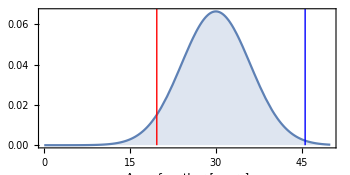

```mathematica
maxLLh=maxLLparams["age_m_h"];
maxLLa=maxLLparams["age_m_a"];
p3=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
ImageSize->350
]
```

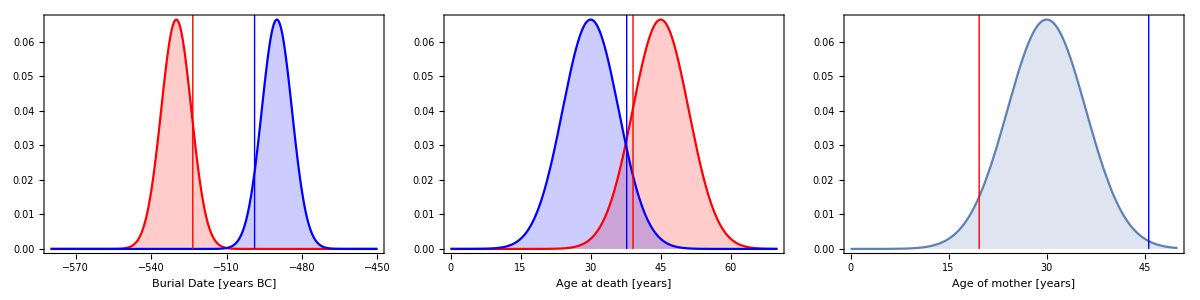

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/sibling_maxLL.pdf",p]
```

Figures/sibling_maxLL.pdf

#### With uncertainty

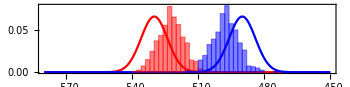

```mathematica
p1=Show[
Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False},
PlotRange->All
],
Histogram[Normal/@{
dat[All,"burial_h"],
dat[All,"burial_a"]
},20,"PDF",ChartStyle->{Red,Blue}
]
,
FrameLabel->{"Burial Date [years BC]",None},
AspectRatio->1/4,
ImageSize->350
]
```

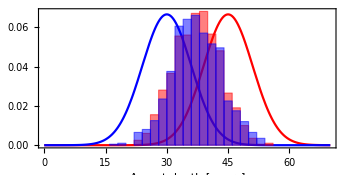

```mathematica
p2=Show[
Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},PlotRange->All
],
Histogram[Normal/@{
dat[All,"age_h"],
dat[All,"age_a"]
},Automatic,"PDF",ChartStyle->{Red,Blue}
],
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
AspectRatio->1/2,
ImageSize->350
]
```

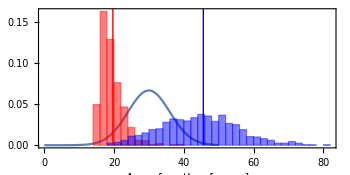

```mathematica
p3=Show[
Plot[PDF[mothersAgeDist,x],{x,0,50}],
Histogram[Normal/@{
dat[All,"age_m_h"],
dat[All,"age_m_a"]
},25,"PDF",ChartStyle->{Red,Blue}
],
Frame->{True,False,False,False},
PlotRange->All,
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
ImageSize->350
]
```

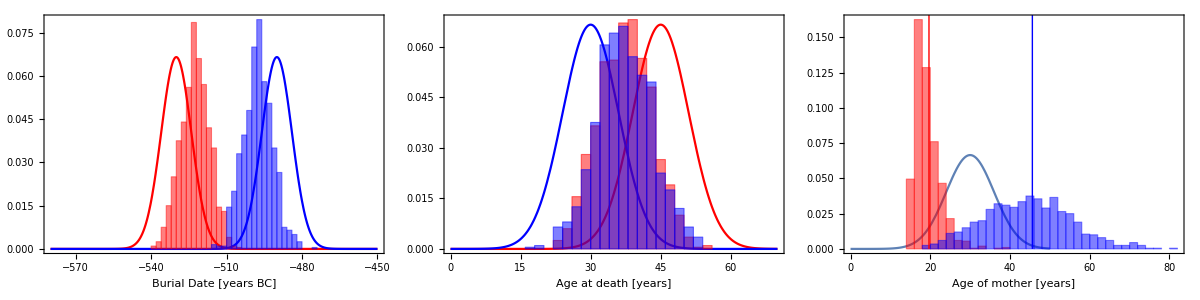

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/sibling_posteriors.pdf",p]
```

Figures/sibling_posteriors.pdf

### Avuncular model

```mathematica
dat=readStanDataset["model_avuncular_output.csv"];
```

```mathematica
dat[First,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_sister,sister_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal
```

<|lp__→19.3623,accept_stat__→0.996511,stepsize__→0.387881,treedepth__→2,n_leapfrog__→7,divergent__→0,energy__→-18.7987,birth_date_mother→-594.706,mother_age_hochdorf→28.39,mother_age_sister→32.9576,sister_age_asperg→35.187,age_hochdorf→42.9703,age_asperg→33.0074,burial_date_hochdorf→-523.345,burial_date_asperg→-493.554|>

```mathematica
maxLLvalue=
LogLikelihood[NormalDistribution[-530,6],{maxLLparams[["burial_date_hochdorf"]]}]+
LogLikelihood[NormalDistribution[-490,6],{maxLLparams[["burial_date_asperg"]]}]+
LogLikelihood[NormalDistribution[45,6],{maxLLparams[["age_hochdorf"]]}]+
LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_asperg"]]}]+LogLikelihood[NormalDistribution[30,6],{maxLLparams[["mother_age_sister"]],maxLLparams[["mother_age_hochdorf"]],maxLLparams[["sister_age_asperg"]]}]
```

-20.4794

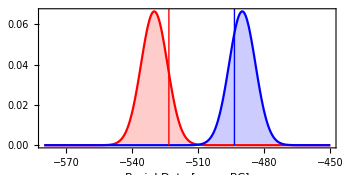

```mathematica
maxLLh=maxLLparams["burial_date_hochdorf"];
maxLLa=maxLLparams["burial_date_asperg"];
p1=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Burial Date [years BC]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

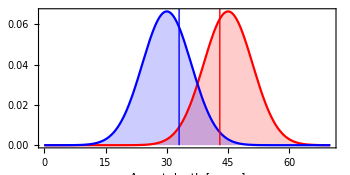

```mathematica
maxLLh=maxLLparams["age_hochdorf"];
maxLLa=maxLLparams["age_asperg"];
p2=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

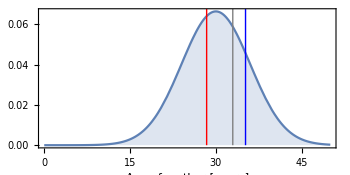

```mathematica
maxLLh=maxLLparams["mother_age_hochdorf"];
maxLLa=maxLLparams["sister_age_asperg"];
maxLLs=maxLLparams["mother_age_sister"];
p3=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}],
Gray,Line[{{maxLLs,0},{maxLLs,1}}]
},
ImageSize->350
]
```

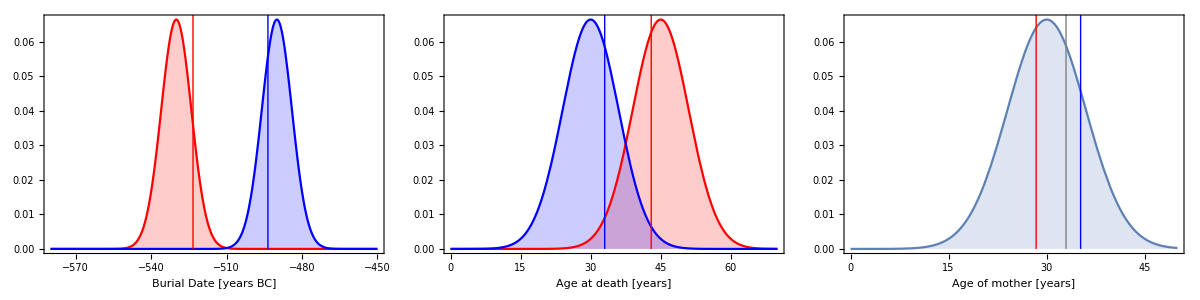

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/avuncular_maxLL.pdf",p]
```

Figures/avuncular_maxLL.pdf

### Cousin model

```mathematica
dat=readStanDataset["model_cousins_output.csv"];
```

```mathematica
dat[First,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_grandmother,grandmother_age_mother_hochdorf,grandmother_age_mother_asperg,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal
```

<|lp__→18.4313,accept_stat__→0.913544,stepsize__→0.373852,treedepth__→3,n_leapfrog__→15,divergent__→0,energy__→-16.3892,birth_date_grandmother→-613.099,grandmother_age_mother_hochdorf→22.8265,grandmother_age_mother_asperg→37.025,mother_age_hochdorf→25.7832,mother_age_asperg→37.3882,age_hochdorf→38.8035,age_asperg→38.5736,burial_date_hochdorf→-525.686,burial_date_asperg→-500.112|>

```mathematica
maxLLvalue=
LogLikelihood[NormalDistribution[-530,6],{maxLLparams[["burial_date_hochdorf"]]}]+
LogLikelihood[NormalDistribution[-490,6],{maxLLparams[["burial_date_asperg"]]}]+
LogLikelihood[NormalDistribution[45,6],{maxLLparams[["age_hochdorf"]]}]+
LogLikelihood[NormalDistribution[30,6],{maxLLparams[["age_asperg"]]}]+LogLikelihood[NormalDistribution[30,6],{maxLLparams[["grandmother_age_mother_hochdorf"]],maxLLparams[["grandmother_age_mother_asperg"]],maxLLparams[["mother_age_hochdorf"]],maxLLparams[["mother_age_asperg"]]}]
```

-27.3237

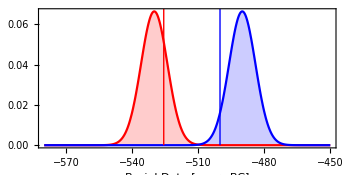

```mathematica
maxLLh=maxLLparams["burial_date_hochdorf"];
maxLLa=maxLLparams["burial_date_asperg"];
p1=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Burial Date [years BC]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

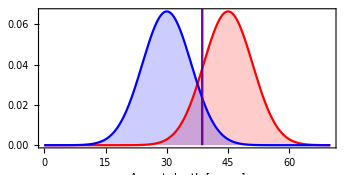

```mathematica
maxLLh=maxLLparams["age_hochdorf"];
maxLLa=maxLLparams["age_asperg"];
p2=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age at death [years]",None},
Epilog->{
Red,Thick,Line[{{maxLLh,0},{maxLLh,1}}],
Blue,Line[{{maxLLa,0},{maxLLa,1}}]
},
AspectRatio->1/2,
ImageSize->350
]
```

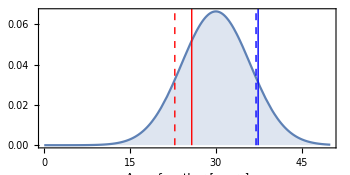

```mathematica
maxLLh1=maxLLparams["grandmother_age_mother_hochdorf"];
maxLLa1=maxLLparams["grandmother_age_mother_asperg"];
maxLLh2=maxLLparams["mother_age_hochdorf"];
maxLLa2=maxLLparams["mother_age_asperg"];
p3=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age of mother [years]",None},
AspectRatio->1/2,
Epilog->{
Red,Thick,Line[{{maxLLh2,0},{maxLLh2,1}}],Dashed,Line[{{maxLLh1,0},{maxLLh1,1}}],
Dashing[None],Blue,Line[{{maxLLa2,0},{maxLLa2,1}}],
Dashed,Line[{{maxLLa1,0},{maxLLa1,1}}]
},
ImageSize->350
]
```

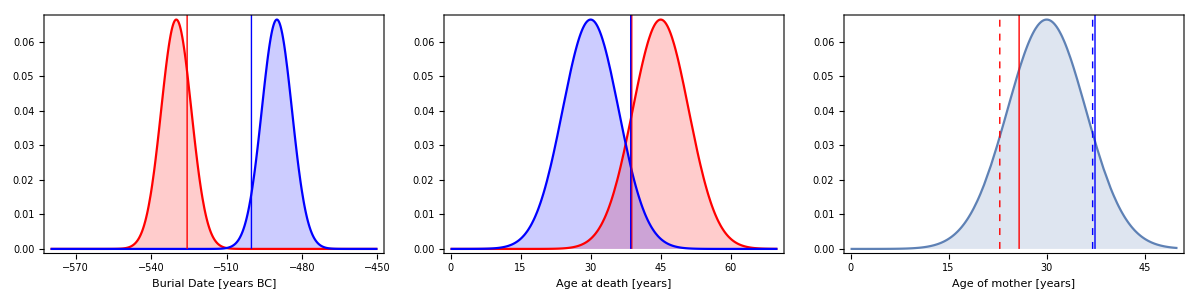

```mathematica
p=Grid[{{p1,p2,p3}}]
```

```mathematica
Export["Figures/cousins_maxLL.pdf",p]
```

Figures/cousins_maxLL.pdf

## Figures for Supplementary Text

```mathematica
plotParam[dat_,param_,dist_,range_,xlabel_]:=Module[{maxLLparams},
maxLLparams=dat[TakeLargestBy["lp__",1]/*First]//Normal;
Show[
Histogram[
dat[All,param],Automatic,"PDF",AspectRatio->1/4,Axes->False,Frame->{True,False,False,False},
FrameLabel->{xlabel,None},
Epilog->{AbsolutePointSize[10], Point[{maxLLparams[[param]],0}]}
],
Plot[PDF[dist,x],{x,Sequence@@range}],
PlotRange->{range,All},
PlotLabel->param,
ImageSize->300
]]
```

```mathematica
dat=readStanDataset["model_siblings_output.csv"];
```

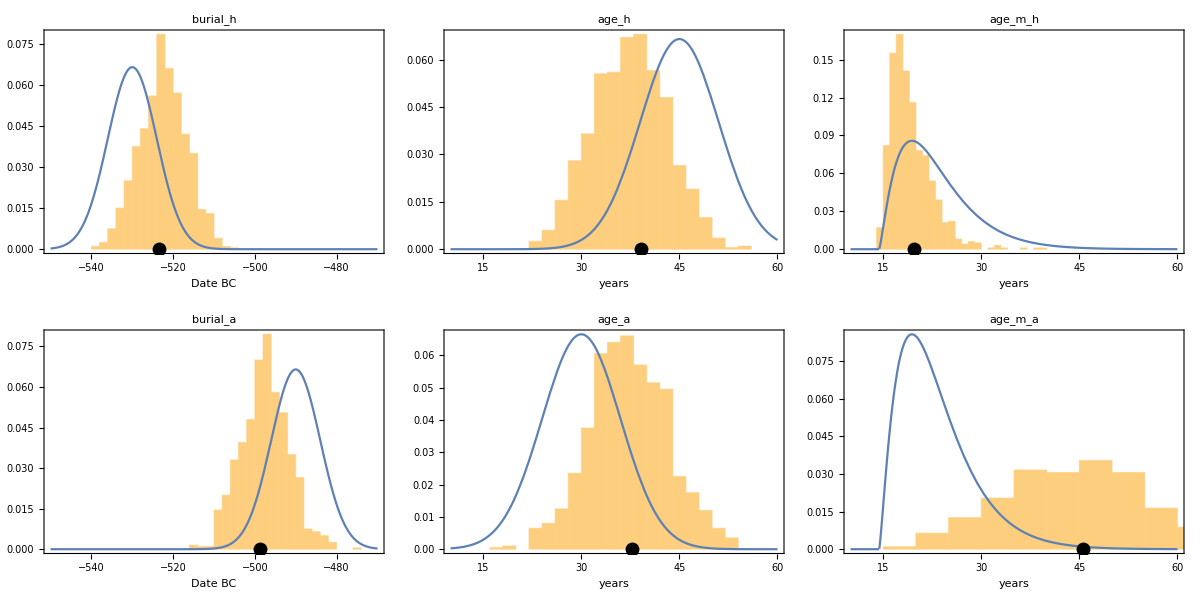

```mathematica
p=Grid@{
{
plotParam[dat,"burial_h",hochdorfBurialDateDist,{-550,-470},"Date BC"],
plotParam[dat,"age_h",hochdorfAgeDist,{10,60},"years"],
plotParam[dat,"age_m_h",mothersAgeDist2,{10,60},"years"]
},
{
plotParam[dat,"burial_a",aspergBurialDateDist,{-550,-470},"Date BC"],
plotParam[dat,"age_a",aspergAgeDist,{10,60},"years"],
plotParam[dat,"age_m_a",mothersAgeDist2,{10,60},"years"]
}
}
```

```mathematica
Export["Figures/sibling_posteriors2.pdf",p]
Export["Figures/sibling_posteriors2.png",p]
```

Figures/sibling_posteriors2.pdf

Figures/sibling_posteriors2.png

```mathematica
dat=readStanDataset["model_avuncular_output.csv"];
```

```mathematica
dat[First,Keys]
```

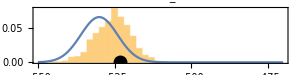
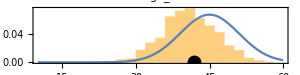
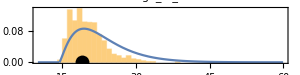
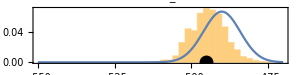
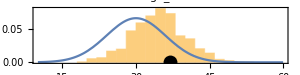
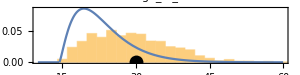
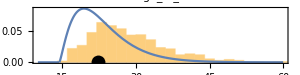
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
 |  | -Graphics-

```mathematica
p=Grid@{
{
plotParam[dat,"burial_h",hochdorfBurialDateDist,{-550,-470},"Date BC"],
plotParam[dat,"age_h",hochdorfAgeDist,{10,60},"years"],
plotParam[dat,"age_m_h",mothersAgeDist2,{10,60},"years"]
},
{
plotParam[dat,"burial_a",aspergBurialDateDist,{-550,-470},"Date BC"],
plotParam[dat,"age_a",aspergAgeDist,{10,60},"years"],
plotParam[dat,"age_m_a",mothersAgeDist2,{10,60},"years"]
},
{
"","",plotParam[dat,"age_m_s",mothersAgeDist2,{10,60},"years"]
}
}
```

```mathematica
Export["Figures/avuncular_posteriors.pdf",p]
Export["Figures/avuncular_posteriors.png",p]
```

Figures/avuncular_posteriors.pdf

Figures/avuncular_posteriors.png

```mathematica
dat=readStanDataset["model_cousins_output.csv"];
```

```mathematica
dat[First,Keys]
```

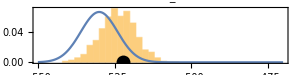
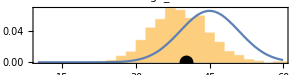
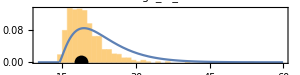
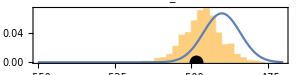
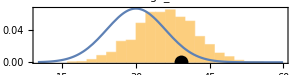
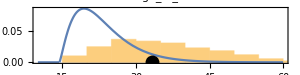
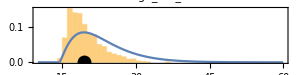
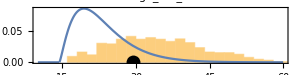
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
p=Grid@{
{
plotParam[dat,"burial_h",hochdorfBurialDateDist,{-550,-470},"Date BC"],
plotParam[dat,"age_h",hochdorfAgeDist,{10,60},"years"],
plotParam[dat,"age_m_h",mothersAgeDist2,{10,60},"years"]
},
{
plotParam[dat,"burial_a",aspergBurialDateDist,{-550,-470},"Date BC"],
plotParam[dat,"age_a",aspergAgeDist,{10,60},"years"],
plotParam[dat,"age_m_a",mothersAgeDist2,{10,60},"years"]
},
{
plotParam[dat,"age_m2_h",mothersAgeDist2,{10,60},"years"],
plotParam[dat,"age_m2_a",mothersAgeDist2,{10,60},"years"]
}
}
```

```mathematica
Export["Figures/cousins_posteriors.pdf",p]
Export["Figures/cousins_posteriors.png",p]
```

Figures/cousins_posteriors.pdf

Figures/cousins_posteriors.png

## Equations

Let L(y|θ) be the likelihood of the data y given parameters θ, and π(θ) be the prior. Then the posterior probability p(θ|y) for parameters θ given data y is

p(θ|y)=(L(y|θ)π(θ))/(∫L(y|θ)π(θ)ⅆθ)=(L(y|θ)π(θ))/M

where we have introduced the “marginal likelihood” M as the normalising constant of the posterior.

### Naive Monte Carlo estimator

For the “Naive Monte Carlo estimator” of M, we produce N prior draws and take the average over the likelihood:

M=∫L(y|θ)π(θ)ⅆθ    =     𝔼_(π(θ))(L(y|θ))    =     1/(N_(prior draws))∑_(i=1)^N L(θ_i)

### Harmonic Mean estimator

We can reorder Bayes Theorem:

p(θ|y)=(L(y|θ)π(θ))/M            ⇒1/M=(p(θ|y))/(L(y|θ)π(θ))

Integrating both sides over the prior:

⇒1/M∫π(θ)ⅆθ=∫(p(θ|y))/(L(y|θ)π(θ))π(θ)ⅆθ=∫1/(L(y|θ))p(θ|y)ⅆθ=𝔼_(p(θ|y))1/(L(y|θ))

so

⇒1/M=𝔼_(p(θ|y))1/(L(y|θ))        ⇒M=(𝔼_(p(θ|y))1/(L(y|θ)))^-1

## Likelihood schema figure

```mathematica
posteriorDist=MultinormalDistribution[{0.5,0.5},{{0.005,0.004},{0.004,0.005}}];
priorDist=ProductDistribution[
UniformDistribution[{0,1}],
UniformDistribution[{0,1}]
];
```

```mathematica
p=Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema.pdf",p]
```

Figures/llFuncSchema.pdf

```mathematica
priorSamples=RandomVariate[priorDist,1000];
```

```mathematica
p=Show[
Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False],
ListPointPlot3D[{#[[1]],#[[2]],PDF[posteriorDist,#[[;;2]]]}&/@priorSamples,PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema2.pdf",p]
```

Figures/llFuncSchema2.pdf

```mathematica
posteriorSamples=RandomVariate[posteriorDist,1000];
```

```mathematica
p=Show[
Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False],
ListPointPlot3D[{#[[1]],#[[2]],PDF[posteriorDist,#[[;;2]]]}&/@posteriorSamples,PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema3.pdf",p]
```

Figures/llFuncSchema3.pdf

```mathematica
points={#[[1]],#[[2]],PDF[posteriorDist,#[[;;2]]]}&/@posteriorSamples;
p=Show[
Plot3D[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All,Axes->None,Boxed->False],
ListPointPlot3D[Select[points,#[[3]]>Median[points[[All,3]]]&],PlotStyle->Red],
ListPointPlot3D[Select[points,#[[3]]<=Median[points[[All,3]]]&],PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Export["Figures/llFuncSchema4.pdf",p]
```

Figures/llFuncSchema4.pdf

## Main Figure

```mathematica
cm=72/2.54;
cmPerCoord=0.9;
textProps={FontSize->8};
rOpts={RoundingRadius->0.1};
x=2.5;
w=0.9;
```

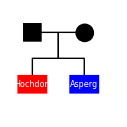

```mathematica
p=Graphics[{
Rectangle[{-w/2,-w/2},{w/2,w/2},Sequence@@rOpts],
Disk[{x,0},w/2],
Line[{{0,0},{x,0}}],
Line[{{x/2,0},{x/2,-x/2},{0,-x/2},{0,-x}}],
Line[{{x/2,0},{x/2,-x/2},{x,-x/2},{x,-x}}],
Red,Rectangle[{-0.8w,-x-w/2},{0.8w,-x+w/2},Sequence@@rOpts],
Blue,Rectangle[{x-0.8w,-x-w/2},{x+0.8w,-x+w/2},Sequence@@rOpts],
White,Text[Style["Hochdorf",Sequence@@textProps],{0,-x}],Text[Style["Asperg",Sequence@@textProps],{x,-x}]
},PlotRange->{{-1,4},{-4,1}},ImageSize->{5 cmPerCoord cm,5cmPerCoord cm}]
```

```mathematica
Export["Figures/tree_sibling.pdf",p]
```

Figures/tree_sibling.pdf

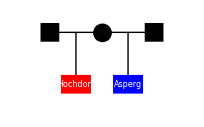

```mathematica
p=Graphics[{
Rectangle[{-x-w/2,-w/2},{-x+w/2,w/2},Sequence@@rOpts],
Disk[{0,0},w/2],
Rectangle[{x-w/2,-w/2},{x+w/2,w/2},Sequence@@rOpts],
Line[{{-x,0},{x,0}}],
Line[{{-x/2,0},{-x/2,-x}}],
Line[{{x/2,0},{x/2,-x}}],
Red,Rectangle[{-x/2-0.8w,-x-w/2},{-x/2+0.8w,-x+w/2},Sequence@@rOpts],
Blue,Rectangle[{x/2-0.8w,-x-w/2},{x/2+0.8w,-x+w/2},Sequence@@rOpts],
White,Text[Style["Hochdorf",Sequence@@textProps],{-x/2,-x}],Text[Style["Asperg",Sequence@@textProps],{x/2,-x}]
},PlotRange->{{-4,4},{-4,1}},ImageSize->{8 cmPerCoord cm,5cmPerCoord cm}]
```

```mathematica
Export["Figures/tree_half_siblings.pdf",p]
```

Figures/tree_half_siblings.pdf

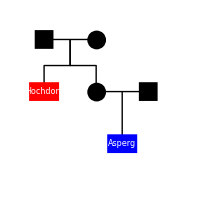

```mathematica
p=Graphics[{
Rectangle[{-w/2,-w/2},{w/2,w/2},Sequence@@rOpts],
Disk[{x,0},w/2],
Line[{{0,0},{x,0}}],
Line[{{x/2,0},{x/2,-x/2},{0,-x/2},{0,-x}}],
Line[{{x/2,0},{x/2,-x/2},{x,-x/2},{x,-x}}],
{Red,Rectangle[{-0.8w,-x-w/2},{0.8w,-x+w/2},Sequence@@rOpts]},
Disk[{x,-x},w/2],
Rectangle[{2x-w/2,-x-w/2},{2x+w/2,-x+w/2},Sequence@@rOpts],
Line[{{x,-x},{2x,-x}}],
Line[{{1.5x,-x},{1.5x,-2x}}],
Blue,Rectangle[{1.5x-0.8w,-2x-w/2},{1.5x+0.8w,-2x+w/2},Sequence@@rOpts],
White,Text[Style["Hochdorf",Sequence@@textProps],{0,-x}],Text[Style["Asperg",Sequence@@textProps],{1.5x,-2x}]
},PlotRange->{{-1.2,7},{-7,1}},ImageSize->{8.2 cmPerCoord cm,8cmPerCoord cm}]
```

```mathematica
Export["Figures/tree_avuncular.pdf",p]
```

Figures/tree_avuncular.pdf

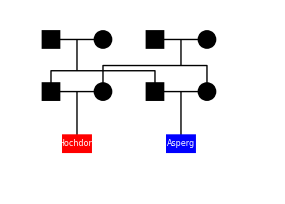

```mathematica
p=Graphics[{
Table[{
Rectangle[{-w/2,y-w/2},{w/2,y+w/2},Sequence@@rOpts],
Disk[{x,y},w/2],
Rectangle[{2x-w/2,y-w/2},{2x+w/2,y+w/2},Sequence@@rOpts],
Disk[{3x,y},w/2],
Line[{{0,y},{x,y}}],Line[{{2x,y},{3x,y}}]
},{y,{0,-x}}
],
Line[{{x,-x},{x,-x/2},{3x,-x/2},{3x,-x}}],
Line[{{0,-x},{0,-0.6x},{2x,-0.6x},{2x,-x}}],
Line[{{x/2,-0.6x},{x/2,0}}],
Line[{{2.5x,-x/2},{2.5x,0}}],
Line[{{x/2,-x},{x/2,-2x}}],Line[{{2.5x,-x},{2.5x,-2x}}],
{Red,Rectangle[{x/2-0.8w,-2x-w/2},{x/2+0.8w,-2x+w/2},Sequence@@rOpts]},
{Blue,Rectangle[{2.5x-0.8w,-2x-w/2},{2.5x+0.8w,-2x+w/2},Sequence@@rOpts]},
White,Text[Style["Hochdorf",Sequence@@textProps],{x/2,-2x}],Text[Style["Asperg",Sequence@@textProps],{2.5x,-2x}]
},PlotRange->{{-1.2,10},{-7,1}},ImageSize->{11.2 cmPerCoord cm,8cmPerCoord cm}]
```

```mathematica
Export["Figures/tree_double_cousins.pdf",p]
```

Figures/tree_double_cousins.pdf